```mathematica
BB[1]=({{0, 0, 0}, {0, 0, 1/(√2)}, {0, 1/(√2), 0}});  
 BB[2]=({{0, 0, 1/(√2)}, {0, 0, 0}, {1/(√2), 0, 0}});
BB[3]=({{0, 1/(√2), 0}, {1/(√2), 0, 0}, {0, 0, 0}});
BB[4]=({{-1/(√2), 0, 0}, {0, 1/(√2), 0}, {0, 0, 0}});BB[5]=1/(√6)({{1, 0, 0}, {0, 1, 0}, {0, 0, -2}}); BB[6]=1/(√3)({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}});
```

```mathematica
DateSequence[date_,WantTime_]:=If[WantTime=="yes",Row[{date⟦2⟧,"-",date⟦3⟧,"-",date⟦1⟧," ",date⟦4⟧,":",date⟦5⟧}],Row[{date⟦2⟧,"-",date⟦3⟧,"-",date⟦1⟧}]];
xyzTP[{θ_,ϕ_}]:={Cos[θ] Sin[ϕ],Sin[θ] Sin[ϕ],Cos[ϕ]};InnerProductMatrix[M_,N_]:=Flatten[M].Flatten[N];
NormMatrix[M_]:=√InnerProductMatrix[M,M];
YRot[t_]:=({{Cos[t], 0, Sin[t]}, {0, 1, 0}, {-Sin[t], 0, Cos[t]}});
ZRot[t_]:=({{Cos[t], -Sin[t], 0}, {Sin[t], Cos[t], 0}, {0, 0, 1}});
UsHat[{θ_,σ_,ϕ_}]:=ZRot[θ].YRot[ϕ].ZRot[σ];  
id=IdentityMatrix[3];
matrixL[L_]:=Table[InnerProductMatrix[L[BB[j]],BB[i]],{i,6},{j,6}]; 
MatrixUbar[U_]:=matrixL[U.#.Transpose[U]&];
```

```mathematica
DistToVΣofU[Tmat_,U_,SymClass_]:=     (* This is d(T,Subscript[V, Σ](U)) in the 2022 paper *)NormMatrix[Transpose[MatrixUbar[U]].Tmat.MatrixUbar[U]-ProjToVSigOfU[Transpose[MatrixUbar[U]].Tmat.MatrixUbar[U],id,SymClass]];
```

#### RefMatrix is a reference matrix for P(T, 𝒱_Σ(U)). It is a reference matrix for T if the symmetry of T is at least Sigma and if U is a Σ-minimizer.

```mathematica
RefMatrix[Tmat_,U_,Sigma_]:=ProjToVSigOfU[Transpose[MatrixUbar[U]].Tmat.MatrixUbar[U],id,Sigma];  (* U should be a Sigma-minimizer for T *)
```

```mathematica
ProjToVSigOfU[Tmat_,U_,Sigma_]:=MatrixUbar[U].ProjToVSigOfU[Transpose[MatrixUbar[U]].Tmat.MatrixUbar[U],id,Sigma].Transpose[MatrixUbar[U]];
```

```mathematica
ProjToVSigOfU[Tmat_,id,TRIV]:=Tmat;   (* These are the P(T,Subscript[V, Σ](I)) in the 2022 paper *)
ProjToVSigOfU[({{a_, g_, m_, q_, t_, v_}, {gdum_, b_, h_, n_, r_, u_}, {mdum_, hdum_, c_, i_, o_, s_}, {qdum_, ndum_, idum_, d_, j_, p_}, {tdum_, rdum_, odum_, jdum_, e_, k_}, {vdum_, udum_, sdum_, pdum_, kdum_, f_}}),id,MONO]:=({{a, g, 0, 0, 0, 0}, {g, b, 0, 0, 0, 0}, {0, 0, c, i, o, s}, {0, 0, i, d, j, p}, {0, 0, o, j, e, k}, {0, 0, s, p, k, f}});
ProjToVSigOfU[({{a_, g_, m_, q_, t_, v_}, {gdum_, b_, h_, n_, r_, u_}, {mdum_, hdum_, c_, i_, o_, s_}, {qdum_, ndum_, idum_, d_, j_, p_}, {tdum_, rdum_, odum_, jdum_, e_, k_}, {vdum_, udum_, sdum_, pdum_, kdum_, f_}}),id,ORTH]:=({{a, 0, 0, 0, 0, 0}, {0, b, 0, 0, 0, 0}, {0, 0, c, 0, 0, 0}, {0, 0, 0, d, j, p}, {0, 0, 0, j, e, k}, {0, 0, 0, p, k, f}});
ProjToVSigOfU[({{a_, g_, m_, q_, t_, v_}, {gdum_, b_, h_, n_, r_, u_}, {mdum_, hdum_, c_, i_, o_, s_}, {qdum_, ndum_, idum_, d_, j_, p_}, {tdum_, rdum_, odum_, jdum_, e_, k_}, {vdum_, udum_, sdum_, pdum_, kdum_, f_}}),id,TRIG]:=({{(a+b)/2, 0, (m+n)/2, 0, 0, 0}, {0, (a+b)/2, 0, (m+n)/2, 0, 0}, {(m+n)/2, 0, (c+d)/2, 0, 0, 0}, {0, (m+n)/2, 0, (c+d)/2, 0, 0}, {0, 0, 0, 0, e, k}, {0, 0, 0, 0, k, f}});
ProjToVSigOfU[({{a_, g_, m_, q_, t_, v_}, {gdum_, b_, h_, n_, r_, u_}, {mdum_, hdum_, c_, i_, o_, s_}, {qdum_, ndum_, idum_, d_, j_, p_}, {tdum_, rdum_, odum_, jdum_, e_, k_}, {vdum_, udum_, sdum_, pdum_, kdum_, f_}}),id,TET]:=({{(a+b)/2, 0, 0, 0, 0, 0}, {0, (a+b)/2, 0, 0, 0, 0}, {0, 0, c, 0, 0, 0}, {0, 0, 0, d, 0, 0}, {0, 0, 0, 0, e, k}, {0, 0, 0, 0, k, f}});
ProjToVSigOfU[({{a_, g_, m_, q_, t_, v_}, {gdum_, b_, h_, n_, r_, u_}, {mdum_, hdum_, c_, i_, o_, s_}, {qdum_, ndum_, idum_, d_, j_, p_}, {tdum_, rdum_, odum_, jdum_, e_, k_}, {vdum_, udum_, sdum_, pdum_, kdum_, f_}}),id,CUBE]:=({{(a+b+c)/3, 0, 0, 0, 0, 0}, {0, (a+b+c)/3, 0, 0, 0, 0}, {0, 0, (a+b+c)/3, 0, 0, 0}, {0, 0, 0, (d+e)/2, 0, 0}, {0, 0, 0, 0, (d+e)/2, 0}, {0, 0, 0, 0, 0, f}});
ProjToVSigOfU[({{a_, g_, m_, q_, t_, v_}, {gdum_, b_, h_, n_, r_, u_}, {mdum_, hdum_, c_, i_, o_, s_}, {qdum_, ndum_, idum_, d_, j_, p_}, {tdum_, rdum_, odum_, jdum_, e_, k_}, {vdum_, udum_, sdum_, pdum_, kdum_, f_}}),id,XISO]:=({{(a+b)/2, 0, 0, 0, 0, 0}, {0, (a+b)/2, 0, 0, 0, 0}, {0, 0, (c+d)/2, 0, 0, 0}, {0, 0, 0, (c+d)/2, 0, 0}, {0, 0, 0, 0, e, k}, {0, 0, 0, 0, k, f}});ProjToVSigOfU[({{a_, g_, m_, q_, t_, v_}, {gdum_, b_, h_, n_, r_, u_}, {mdum_, hdum_, c_, i_, o_, s_}, {qdum_, ndum_, idum_, d_, j_, p_}, {tdum_, rdum_, odum_, jdum_, e_, k_}, {vdum_, udum_, sdum_, pdum_, kdum_, f_}}),id,ISO]:=({{(a+b+c+d+e)/5, 0, 0, 0, 0, 0}, {0, (a+b+c+d+e)/5, 0, 0, 0, 0}, {0, 0, (a+b+c+d+e)/5, 0, 0, 0}, {0, 0, 0, (a+b+c+d+e)/5, 0, 0}, {0, 0, 0, 0, (a+b+c+d+e)/5, 0}, {0, 0, 0, 0, 0, f}});
```

```mathematica
GetTempAndθ0σ0ϕ0[Tmat_,Sigma_]:=(
If[MemberQ[{ISO},Sigma],
temp={DistToVΣofU[Tmat,UsHat[{0.,0,0}],Sigma],{θ->0,σ->0,ϕ->0}},
temp= NMinimize[{DistToVΣofU[Tmat,UsHat[{θ,σ,ϕ}],Sigma],0≤θ≤2π&&-π≤σ≤π&&0≤ϕ≤π},{θ,σ,ϕ},Method->"RandomSearch"]];
{θ0,σ0,ϕ0}=({θ,σ,ϕ}/.temp[[2]]);)
GetTempAndθ0σ0ϕ0[Tmat_,XISO]:=(
temp=NMinimize[{DistToVΣofU[Tmat,UsHat[{θ,0.,ϕ}],XISO],0≤θ≤2π&&0≤ϕ≤π},{θ,ϕ},Method->"RandomSearch"];
θ0=θ/.temp[[2,1]];
σ0=0;
ϕ0=ϕ/.temp[[2,2]];)
GetTempAndθ0σ0ϕ0[Tmat_,MONO]:=(
temp=NMinimize[{DistToVΣofU[Tmat,UsHat[{θ,0.,ϕ}],MONO],0≤θ≤2π&&0≤ϕ≤π},{θ,ϕ},Method->"RandomSearch"];
θ0=θ/.temp[[2,1]];
σ0=0;
ϕ0=ϕ/.temp[[2,2]];)
```

```mathematica
OutputFor[Tmat_,Sigma_]:=(Clear[θ,σ,ϕ];
Print[DateSequence[DateList[],"yes"]];
GetTempAndθ0σ0ϕ0[Tmat,Sigma];
Print[temp,"  ( minimizing the function  (θ,σ,ϕ) ",Style["⟶" ,Bold,14]," d",Style["(",18],"T, ",SubscriptBox[Style["𝒱",14,Bold],Sigma]//DisplayForm,"(U)",Style[")",18],", U = (Û)_S(θ,σ,ϕ) )" ];
UT[Tmat,Sigma]=UsHat[{θ0,σ0,ϕ0}];
dT[Tmat,Sigma]=temp[[1]]; (* NormMatrix[Tmat] removed Oct 2021 *)
βT[Tmat,Sigma]=Chop[ArcSin[temp[[1]]/NormMatrix[Tmat]],ChopTol];
Print["       ( {θ, σ, ϕ} in degrees are ",{θ0,σ0,ϕ0}/Degree ," )"];
Print["d(T, ",SubscriptBox[Style["𝒯",Bold],Sigma]//DisplayForm,") = ",Chop[temp[[1]],ChopTol]," ( distance from T to ",SubscriptBox[Style["𝒯",Bold],Sigma]//DisplayForm," )"];

Print[SubsuperscriptBox["β",Sigma,"T"]//DisplayForm," = ",βT[Tmat,Sigma]," = ",(βT[Tmat,Sigma]/Degree)^o," ( angle between T and ",SubscriptBox[Style["𝒯",Bold],Sigma]//DisplayForm," )"];

Print["U = (Û)_S(θ,σ,ϕ) = ",MatrixForm[Chop[ UT[Tmat,Sigma],ChopTol]],"  ( minimizes the function  U ",Style["⟶" ,Bold,14]," d",Style["(",18],"T, ",SubscriptBox[Style["𝒱",14,Bold],Sigma]//DisplayForm,"(U)",Style[")",18]," )"];

Print["P",Style["(",18],"T, ",SubscriptBox[Style["𝒱",14,Bold],Sigma]//DisplayForm,"(U)",Style[")",18],If[NormMatrix[Tmat-ProjToVSigOfU[Tmat,UT[Tmat,Sigma],Sigma]]<.00001,Style[" = T",Red,Bold,14],
SequenceForm[" = ",MatrixForm[Round[ProjToVSigOfU[Tmat,UT[Tmat,Sigma],Sigma],.001]]]],"  (a closest elastic map to T having symmetry at least ",Sigma,")"];

Print[SubscriptBox["T",Sigma]//DisplayForm," = P",Style["(",20],"[Ū]^T T [Ū], ",SubscriptBox[Style["𝒱",14,Bold],Sigma]//DisplayForm,"(I)",Style[")",20]," = ",MatrixForm[Round[RefMatrix[Tmat,UT[Tmat,Sigma],Sigma],.001]],"  ( a ",Sigma,"-ref matrix for ","P",Style["(",18],"T, ",SubscriptBox[Style["𝒱",14,Bold],Sigma]//DisplayForm,"(U)",Style[")",18]];)
```

```mathematica
βT[Tmat_,TRIV]:=0;
```

```mathematica
RoundMaybe[dSig_]:=If[dSig==0,0,If[dSig==999,999,Round[dSig,.1]^("o")]]; (* change the rounding if desired *)
```

```mathematica
seq[Sig_,dSig_]:=SequenceForm[Subsuperscript[Style["β",22],Style[Sig,14],Overscript[Style[" ",5],Style["T",Bold,15]]],Style[" = ",20],Style[RoundMaybe[dSig],20]];
```

```mathematica
LatticeOfDTs[Tmat_]:=(ww=1.7;
Print["ChopTol = ",ChopTol];
Graphics[{Arrowheads[.08],Thickness[.006],
{If[βT[Tmat,MONO]==0,Red],Arrow[{{0,-.13},{0,1}},.25]},  (* from TRIV to MONO *)
{If[βT[Tmat,ORTH]==0,Red],Arrow[{{0,1},{1ww,2}},.5]},  (* from MONO to ORTH *)
{If[βT[Tmat,TET]==0,Red],  Arrow[{{   1ww,1.9},{1ww,3}},.2]},   (* from ORTH *)
{If[βT[Tmat,CUBE]==0,Red],Arrow[{{  1ww,2.9},{   1ww,4}},.2]},   (* from TET to CUBE *)
{If[βT[Tmat,XISO]==0,Red],Arrow[{{-1ww,2.9},{-1ww,4}},.2]},   (* from TRIG to XISO *)
{If[βT[Tmat,CUBE]==0,Red],Arrow[{{-1ww,3},{   1ww,4}},.8]},   (* from TRIG to CUBE *)
{If[βT[Tmat,XISO]==0,Red],Arrow[{{   1ww,3},{-1ww,4}},.7]},   (* from TET to XISO *)
{If[βT[Tmat,TRIG]==0,Red],Arrow[{{0,1},{-1ww,3}},.3]},   (* from MONO to TRIG *)
{If[βT[Tmat,ISO]==0,Red],Arrow[{{   1ww,4},{0,5}},.5]},   (* from CUBE to ISO *)
{If[βT[Tmat,ISO]==0,Red],Arrow[{{-1ww,4},{0,5}},.55]},   (* from XISO to ISO *)
Text[seq[TRIV,βT[Tmat,TRIV]/Degree],{0,0}],
Text[seq[MONO,βT[Tmat,MONO]/Degree],{0,1}],
Text[seq[ORTH,βT[Tmat,ORTH]/Degree],{1ww,2}],
Text[seq[TET,  βT[Tmat,TET]/Degree],  {   1ww,3}],
Text[seq[CUBE,βT[Tmat,CUBE]/Degree],{   1ww,4}],
Text[seq[XISO,βT[Tmat,XISO]/Degree],{-1ww,4}],
Text[seq[TRIG,βT[Tmat,TRIG]/Degree],{-1ww,3}],
Text[seq[ISO,  βT[Tmat,ISO]/Degree],{0,5}]},AspectRatio->Automatic])
```

```mathematica
dT[Tmat_,Sigma_]:=999
βT[Tmat_,Sigma_]:=999Degree
```

#### The TET example from Section 15.3 of TapeTape2021. Change Tmat to suit yourself.

```mathematica
Print[DateSequence[DateList[],"yes"]];
Tmat=1/64({{168, 4 √6, -40, 6 √6, 6 √2, 0}, {4 √6, 324, -4 √6, -42, -14 √3, 16 √3}, {-40, -4 √6, 168, -6 √6, -6 √2, 0}, {6 √6, -42, -6 √6, 233, 35 √3, -8 √3}, {6 √2, -14 √3, -6 √2, 35 √3, 163, -8}, {0, 16 √3, 0, -8 √3, -8, 352}});
denominator=64;
```

12-5-2021 15:49

```mathematica
ChopTol=.00001;    (*  d(T, Subscript[𝒯, Σ])is set to zero if it is less than ChopTol; change if desired *)
```

## In what follows, only β and U are needed if only the symmetry group of T is wanted.

#### Σ = MONO

```mathematica
OutputFor[Tmat,MONO]
```

12-5-2021 15:49

{7.522×10^-8,{θ→1.75805,ϕ→1.38675}}  ( minimizing the function  (θ,σ,ϕ) ⟶ d(T, 𝒱_MONO(U)), U = (Û)_S(θ,σ,ϕ) )

( {θ, σ, ϕ} in degrees are {100.729,0,79.4547} )

d(T, 𝒯_MONO) = 0 ( distance from T to 𝒯_MONO )

β_MONO^T = 0 = 0^o ( angle between T and 𝒯_MONO )

U = (Û)_S(θ,σ,ϕ) = (-0.0340691 | -0.98252 | -0.183013
0.179814 | -0.186157 | 0.965926
-0.983111 | 0 | 0.183013)  ( minimizes the function  U ⟶ d(T, 𝒱_MONO(U)) )

P(T, 𝒱_MONO(U)) = T  (a closest elastic map to T having symmetry at least MONO)

T_MONO = P([Ū]^T T [Ū], 𝒱_MONO(I)) = (2.517 | -0.5 | 0. | 0. | 0. | 0.
-0.5 | 2.483 | 0. | 0. | 0. | 0.
0. | 0. | 5.121 | -0.108 | 0.649 | 0.433
0. | 0. | -0.108 | 2.004 | -0.023 | -0.015
0. | 0. | 0.649 | -0.023 | 4.375 | 0.25
0. | 0. | 0.433 | -0.015 | 0.25 | 5.5)  ( a MONO-ref matrix for P(T, 𝒱_MONO(U))

#### Σ = ORTH

```mathematica
OutputFor[Tmat,ORTH]
```

12-5-2021 15:49

{5.86724×10^-8,{θ→3.14159,σ→-1.0472,ϕ→2.35619}}  ( minimizing the function  (θ,σ,ϕ) ⟶ d(T, 𝒱_ORTH(U)), U = (Û)_S(θ,σ,ϕ) )

( {θ, σ, ϕ} in degrees are {180.,-60.,135.} )

d(T, 𝒯_ORTH) = 0 ( distance from T to 𝒯_ORTH )

β_ORTH^T = 0 = 0^o ( angle between T and 𝒯_ORTH )

U = (Û)_S(θ,σ,ϕ) = (0.353553 | 0.612372 | -0.707107
0.866025 | -0.5 | 0
-0.353553 | -0.612372 | -0.707107)  ( minimizes the function  U ⟶ d(T, 𝒱_ORTH(U)) )

P(T, 𝒱_ORTH(U)) = T  (a closest elastic map to T having symmetry at least ORTH)

T_ORTH = P([Ū]^T T [Ū], 𝒱_ORTH(I)) = (2. | 0. | 0. | 0. | 0. | 0.
0. | 2. | 0. | 0. | 0. | 0.
0. | 0. | 4. | 0. | 0. | 0.
0. | 0. | 0. | 3. | 0. | 0.
0. | 0. | 0. | 0. | 5.5 | -0.5
0. | 0. | 0. | 0. | -0.5 | 5.5)  ( a ORTH-ref matrix for P(T, 𝒱_ORTH(U))

#### Σ = TET

```mathematica
OutputFor[Tmat,TET]
```

12-5-2021 15:50

{8.82382×10^-8,{θ→3.14159,σ→2.87979,ϕ→2.35619}}  ( minimizing the function  (θ,σ,ϕ) ⟶ d(T, 𝒱_TET(U)), U = (Û)_S(θ,σ,ϕ) )

( {θ, σ, ϕ} in degrees are {180.,165.,135.} )

d(T, 𝒯_TET) = 0 ( distance from T to 𝒯_TET )

β_TET^T = 0 = 0^o ( angle between T and 𝒯_TET )

U = (Û)_S(θ,σ,ϕ) = (-0.683013 | -0.183013 | -0.707107
-0.258819 | 0.965926 | 0
0.683013 | 0.183013 | -0.707107)  ( minimizes the function  U ⟶ d(T, 𝒱_TET(U)) )

P(T, 𝒱_TET(U)) = T  (a closest elastic map to T having symmetry at least TET)

T_TET = P([Ū]^T T [Ū], 𝒱_TET(I)) = (2. | 0. | 0. | 0. | 0. | 0.
0. | 2. | 0. | 0. | 0. | 0.
0. | 0. | 3. | 0. | 0. | 0.
0. | 0. | 0. | 4. | 0. | 0.
0. | 0. | 0. | 0. | 5.5 | -0.5
0. | 0. | 0. | 0. | -0.5 | 5.5)  ( a TET-ref matrix for P(T, 𝒱_TET(U))

#### Σ = CUBE

```mathematica
OutputFor[Tmat,CUBE]
```

12-5-2021 15:50

{1.51383,{θ→1.75805,σ→-0.802729,ϕ→1.38675}}  ( minimizing the function  (θ,σ,ϕ) ⟶ d(T, 𝒱_CUBE(U)), U = (Û)_S(θ,σ,ϕ) )

( {θ, σ, ϕ} in degrees are {100.729,-45.993,79.4547} )

d(T, 𝒯_CUBE) = 1.51383 ( distance from T to 𝒯_CUBE )

β_CUBE^T = 0.156781 = 8.98287^o ( angle between T and 𝒯_CUBE )

U = (Û)_S(θ,σ,ϕ) = (0.683013 | -0.707107 | -0.183013
0.258819 | 0 | 0.965926
-0.683013 | -0.707107 | 0.183013)  ( minimizes the function  U ⟶ d(T, 𝒱_CUBE(U)) )

P(T, 𝒱_CUBE(U)) = (2.635 | 0.37 | -0.302 | 0.555 | 0.32 | 0.
0.37 | 4.599 | -0.37 | -0.227 | -0.131 | 0.
-0.302 | -0.37 | 2.635 | -0.555 | -0.32 | 0.
0.555 | -0.227 | -0.555 | 3.806 | 0.85 | 0.
0.32 | -0.131 | -0.32 | 0.85 | 2.824 | 0.
0. | 0. | 0. | 0. | 0. | 5.5)  (a closest elastic map to T having symmetry at least CUBE)

T_CUBE = P([Ū]^T T [Ū], 𝒱_CUBE(I)) = (2.333 | 0. | 0. | 0. | 0. | 0.
0. | 2.333 | 0. | 0. | 0. | 0.
0. | 0. | 2.333 | 0. | 0. | 0.
0. | 0. | 0. | 4.75 | 0. | 0.
0. | 0. | 0. | 0. | 4.75 | 0.
0. | 0. | 0. | 0. | 0. | 5.5)  ( a CUBE-ref matrix for P(T, 𝒱_CUBE(U))

#### Σ = TRIG

```mathematica
OutputFor[Tmat,TRIG]
```

12-5-2021 15:51

{0.707107,{θ→0.,σ→-2.07063,ϕ→0.785398}}  ( minimizing the function  (θ,σ,ϕ) ⟶ d(T, 𝒱_TRIG(U)), U = (Û)_S(θ,σ,ϕ) )

( {θ, σ, ϕ} in degrees are {0.,-118.639,45.} )

d(T, 𝒯_TRIG) = 0.707107 ( distance from T to 𝒯_TRIG )

β_TRIG^T = 0.0729973 = 4.18244^o ( angle between T and 𝒯_TRIG )

U = (Û)_S(θ,σ,ϕ) = (-0.338904 | 0.6206 | 0.707107
-0.877661 | -0.479282 | 0
0.338904 | -0.6206 | 0.707107)  ( minimizes the function  U ⟶ d(T, 𝒱_TRIG(U)) )

P(T, 𝒱_TRIG(U)) = (2.75 | 0. | -0.75 | 0. | 0. | 0.
0. | 5. | 0. | -0.75 | -0.433 | 0.433
-0.75 | 0. | 2.75 | 0. | 0. | 0.
0. | -0.75 | 0. | 3.5 | 0.866 | -0.217
0. | -0.433 | 0. | 0.866 | 2.5 | -0.125
0. | 0.433 | 0. | -0.217 | -0.125 | 5.5)  (a closest elastic map to T having symmetry at least TRIG)

T_TRIG = P([Ū]^T T [Ū], 𝒱_TRIG(I)) = (2. | 0. | 0. | 0. | 0. | 0.
0. | 2. | 0. | 0. | 0. | 0.
0. | 0. | 3.5 | 0. | 0. | 0.
0. | 0. | 0. | 3.5 | 0. | 0.
0. | 0. | 0. | 0. | 5.5 | -0.5
0. | 0. | 0. | 0. | -0.5 | 5.5)  ( a TRIG-ref matrix for P(T, 𝒱_TRIG(U))

#### Σ = XISO

```mathematica
OutputFor[Tmat,XISO]
```

12-5-2021 15:51

{0.707107,{θ→0.,ϕ→0.785398}}  ( minimizing the function  (θ,σ,ϕ) ⟶ d(T, 𝒱_XISO(U)), U = (Û)_S(θ,σ,ϕ) )

( {θ, σ, ϕ} in degrees are {0.,0,45.} )

d(T, 𝒯_XISO) = 0.707107 ( distance from T to 𝒯_XISO )

β_XISO^T = 0.0729973 = 4.18244^o ( angle between T and 𝒯_XISO )

U = (Û)_S(θ,σ,ϕ) = (0.707107 | 0 | 0.707107
0 | 1. | 0
-0.707107 | 0 | 0.707107)  ( minimizes the function  U ⟶ d(T, 𝒱_XISO(U)) )

P(T, 𝒱_XISO(U)) = (2.75 | 0. | -0.75 | 0. | 0. | 0.
0. | 5. | 0. | -0.75 | -0.433 | 0.433
-0.75 | 0. | 2.75 | 0. | 0. | 0.
0. | -0.75 | 0. | 3.5 | 0.866 | -0.217
0. | -0.433 | 0. | 0.866 | 2.5 | -0.125
0. | 0.433 | 0. | -0.217 | -0.125 | 5.5)  (a closest elastic map to T having symmetry at least XISO)

T_XISO = P([Ū]^T T [Ū], 𝒱_XISO(I)) = (2. | 0. | 0. | 0. | 0. | 0.
0. | 2. | 0. | 0. | 0. | 0.
0. | 0. | 3.5 | 0. | 0. | 0.
0. | 0. | 0. | 3.5 | 0. | 0.
0. | 0. | 0. | 0. | 5.5 | -0.5
0. | 0. | 0. | 0. | -0.5 | 5.5)  ( a XISO-ref matrix for P(T, 𝒱_XISO(U))

#### Σ = ISO

```mathematica
OutputFor[Tmat,ISO]
```

12-5-2021 15:51

{3.04959,{θ→0,σ→0,ϕ→0}}  ( minimizing the function  (θ,σ,ϕ) ⟶ d(T, 𝒱_ISO(U)), U = (Û)_S(θ,σ,ϕ) )

( {θ, σ, ϕ} in degrees are {0,0,0} )

d(T, 𝒯_ISO) = 3.04959 ( distance from T to 𝒯_ISO )

β_ISO^T = 0.319973 = 18.3331^o ( angle between T and 𝒯_ISO )

U = (Û)_S(θ,σ,ϕ) = (1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)  ( minimizes the function  U ⟶ d(T, 𝒱_ISO(U)) )

P(T, 𝒱_ISO(U)) = (3.3 | 0. | 0. | 0. | 0. | 0.
0. | 3.3 | 0. | 0. | 0. | 0.
0. | 0. | 3.3 | 0. | 0. | 0.
0. | 0. | 0. | 3.3 | 0. | 0.
0. | 0. | 0. | 0. | 3.3 | 0.
0. | 0. | 0. | 0. | 0. | 5.5)  (a closest elastic map to T having symmetry at least ISO)

T_ISO = P([Ū]^T T [Ū], 𝒱_ISO(I)) = (3.3 | 0. | 0. | 0. | 0. | 0.
0. | 3.3 | 0. | 0. | 0. | 0.
0. | 0. | 3.3 | 0. | 0. | 0.
0. | 0. | 0. | 3.3 | 0. | 0.
0. | 0. | 0. | 0. | 3.3 | 0.
0. | 0. | 0. | 0. | 0. | 5.5)  ( a ISO-ref matrix for P(T, 𝒱_ISO(U))

ChopTol = 0.00001

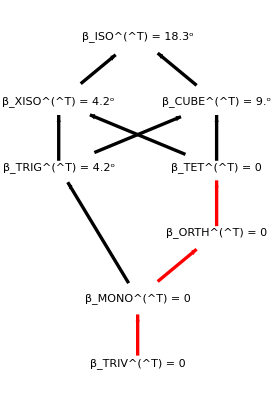

[T] = 1/64(168 | 4 √6 | -40 | 6 √6 | 6 √2 | 0
4 √6 | 324 | -4 √6 | -42 | -14 √3 | 16 √3
-40 | -4 √6 | 168 | -6 √6 | -6 √2 | 0
6 √6 | -42 | -6 √6 | 233 | 35 √3 | -8 √3
6 √2 | -14 √3 | -6 √2 | 35 √3 | 163 | -8
0 | 16 √3 | 0 | -8 √3 | -8 | 352)

```mathematica
LatticeOfDTs[Tmat]
Print["[T] = ",1/denominator,MatrixForm[denominator Tmat]]
```

#### From the lattice and the appropriate U_Σ you get the symmetry group of T. See Theorem 4 of TapeTape2022.